```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
```

```mathematica
figureNameSensitivity ="sensitivity";
figureDirectorySensitivity = figureNameSensitivity;
```

```mathematica
sensitivityPars={αC,αP,αN,αU,βP,βN,ϕN,δN(*,ini[c],ini[p],ini[n0]*)};
minSensitivityRange=0;
maxSensitivityRange=2;
```

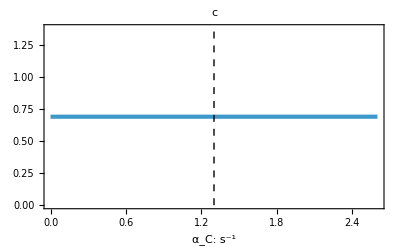
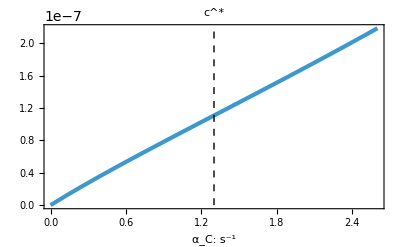
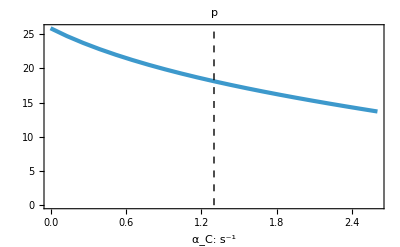
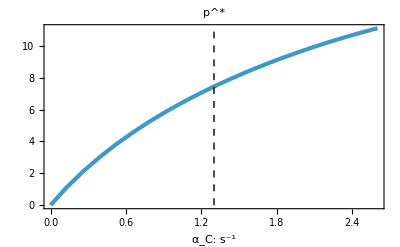
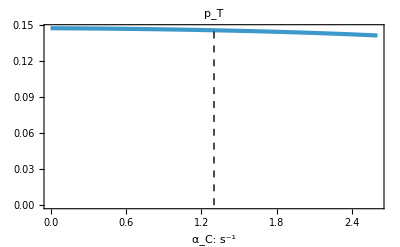
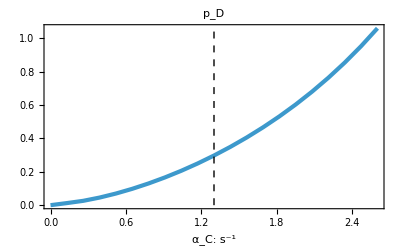
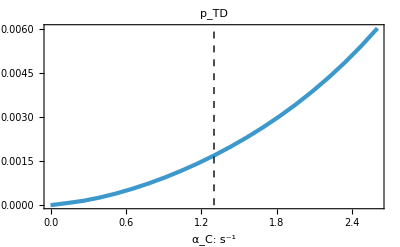
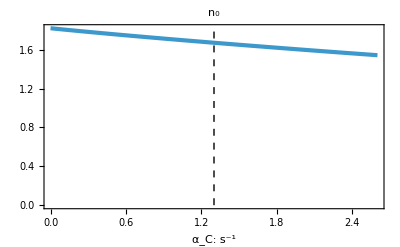
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[Table[(Export[NotebookDirectory[]<>"export/"<>figureDirectorySensitivity<>"/"<>figureNameSensitivity<>"_"<>(sensitivityPar/.namesUTF8)<>".pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],sensitivityPar,Table[i sensitivityPar/.pars[0],{i,minSensitivityRange,maxSensitivityRange,.1}],{#}, 24 3600,{FrameLabel->{{None,None},{Row[{sensitivityPar/.names,": ",sensitivityPar/.units}],None}},Epilog->{Black,Dashed,Line[{{sensitivityPar/.pars[0],0},{sensitivityPar/.pars[0],10^5}}]},PlotRange->Full,AxesOrigin->{Automatic,0},PlotLabel->(#/.names)}]&,quants],{sensitivityPar,sensitivityPars}]]
```